# Machine Learning the Optimal Cryptocurrency Portfolio from Blockchain Activity

Shivain Vij

Philip Maymin

Cryptocurrencies are notoriously unpredictable with traditional financial approaches. This project will utilize historical blockchain activity to construct a machine learning algorithm that would be able to optimize intraday cryptocurrency portfolio allocations. The results would be compared to traditional financial approaches to identify the success rate of the machine learned algorithm.


DATA TO COLLECT:
- Volatility & Price


1. Identify relations between stocks and see if they all go up or down at the same time <-- DONE
2. Import optimized data for past 10 years for 5 Cryptocurrencies {}
3.  Import BlockchainData for past 10 years for 5 Cryptocurrencies  {} <- t
4. Machine Learning Algorithm

```mathematica
btc = FinancialData["BTC/USD",{2016, 07, 18}];
eth = FinancialData["ETH/USD", {2008, 1, 1}];
ImageDifference[DateListPlot[eth], DateListPlot[btc]]
```

The above graph shows that Bitcoin and Ethereum’s prices fluctuate in similar patterns

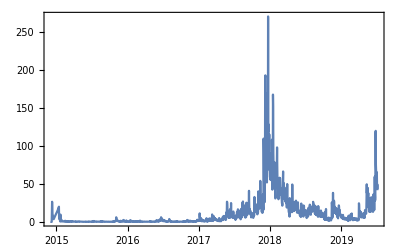

```mathematica
stddev = Drop[Flatten[Import["bitcoinity_data.xlsx"]],2];
volatility= ArrayReshape[stddev, {1640, 2}];
DateListPlot[volatility, PlotRange->All]
```

```mathematica
portfolio={"BTC","ETH"};
data =FinancialData[#, {{2010},{2020}}]&/@portfolio
returns=Differences@*Log/@data


NMinimize

Risk Parity














Read
```

SCRAP CODE BELOW

```mathematica
ToExpression/@(StringReplace[#,","->""]&/@BTCData[[2;;, 2]])// Normal;
BTCData[[2;;, 1]]//Normal;
Riffle[ToExpression/@(StringReplace[#,","->""]&/@BTCData[[2;;, 2]])// Normal, BTCData[[2;;, 1]]//Normal]
```

Dataset[<>]

```mathematica
BlockchainTransactionData[BlockchainBlockData[1000000]["TransactionList"]]//Dataset
```

Dataset[<>]

```mathematica
stddev = Drop[Flatten[Import["bitcoinity_data.xlsx"]],2];
portfolio={"BTC","ETH"};
data =FinancialData[#, {{2010},{2020}}]&/@portfolio
returns=Differences@*Log/@data
MatrixForm[stddev, [[2, 2]]]

ListLinePlot[returns, PlotRange -> All]
Optimization


Select[Table[(BlockchainTransactionData[BlockchainBlockData[x]["TransactionList"]]//Dataset)[[1,8]], {x, 1}], # ≠ Quantity[50., "Bitcoins"]&]
DateListPlot[({Interpreter["DateTime"][First[#]],Last[#]})&/@Table[ArrayReshape[StringSplit[btcJuly,{",","\t","\n"}],{1827,12}][[x]][[{1,12}]], {x, 2, 10}]]
ArrayReshape[StringSplit[stddev,{" ","\t","\n"}],{1641,2}][[x]][[{1,2}]]
```

{TimeSeries[…],TimeSeries[…]}

{TimeSeries[…],TimeSeries[…]}

```mathematica
data=FinancialData[#,"Price",{{2016},{2017},"Month"}][[All,2]]&/@Portfolio;
```

Part::partd: Part specification … is longer than depth of object.

Differences::listrp: List or SparseArray or StructuredArray expected at position 1 in Differences[Log[TemporalData[TimeSeries,{{{380.828,430.92,413.715,456.42,526.24,633.33,653.72,575.555,605.08,693.125,730.975,959.13,963.88}},{{{«13»}}},1,{Discrete,1},{Discrete,1},1,{ValueDimensions→1,DateFunction→Automatic,MetaInformation→{«1»},ResamplingMethod→{«2»},TemporalRegularity→Automatic}},True,12.]⟦All,2⟧]].

Differences::listrp: List or SparseArray or StructuredArray expected at position 1 in Differences[Log[TemporalData[TimeSeries,{{{12.44,11.2,13.1879,10.9491,8.58691,8.14838,8.11922}},{{{«7»}}},1,{Discrete,1},{Discrete,1},1,{ValueDimensions→1,DateFunction→Automatic,MetaInformation→{«1»},ResamplingMethod→{«2»},TemporalRegularity→Automatic}},True,12.]⟦All,2⟧]].

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

ReplaceAll::reps: {Rule[«2»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

General::stop: Further output of Rule::argr will be suppressed during this calculation.

Part::partw: Part 3 of … does not exist.

Differences::listrp: List or SparseArray or StructuredArray expected at position 1 in Differences[Log[{TemporalData[TimeSeries,{{«1»},{«1»},1,{«2»},{«2»},1,{«5»}},True,12.]⟦All,2⟧,TemporalData[TimeSeries,{{«1»},{«1»},1,{«2»},{«2»},1,{«5»}},True,12.]⟦All,2⟧}⟦3⟧]].

General::stop: Further output of Differences::listrp will be suppressed during this calculation.

Part::partd: Part specification … is longer than depth of object.

Part::partw: Part 4 of … does not exist.

Part::partd: Part specification … is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 5 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.